```mathematica
rhoM=0.271;
rhoR=8.4*^-5;
rhoL=1-rhoM-rhoR;
```

```mathematica
Clear[rhoM,rhoR,rhoL]
```

```mathematica
DSolve[(D[a[t],t]^2/a[t]^2==0rhoM/a[t]^3+(1/2)/a[t]^4+1/2),a[t],t,Assumptions->rhoL>0&&rhoR>0]
```

{{a[t]→-√(-Sinh[√2 t-2 C[1]])},{a[t]→√(-Sinh[√2 t-2 C[1]])},{a[t]→-√Sinh[√2 t+2 C[1]]},{a[t]→√Sinh[√2 t+2 C[1]]}}

```mathematica
asol[t_]:=√Sinh[t]
```

```mathematica
conf[t_]:=Integrate[1/asol[T],{T,0,t}]
```

```mathematica
aconf[t_]:=(-1+ⅈ) (√2 EllipticF[1/4 (π-2 ⅈ t),2]-EllipticK[1/2]);
```

```mathematica
nconf[t_]:=NIntegrate[1/asol[T],{T,0,t}]
```

```mathematica
hubb[t_]:=Coth[t]/2
```

```mathematica
time[n_]:=-1/2 ⅈ (π+4 JacobiAmplitude[((1+ⅈ) n-2 EllipticK[1/2])/(2 √2),2])
```

```mathematica
D[asol[t],t]/asol[t]
```

Coth[t]/2

```mathematica
cohub[t_]:=asol[t]hubb[t]
```

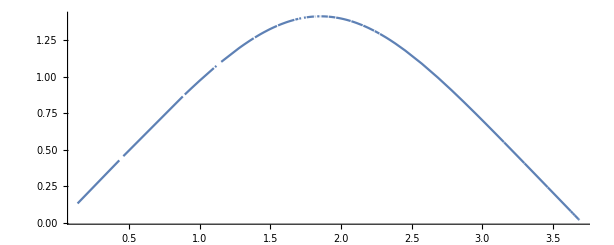

```mathematica
ParametricPlot[{aconf[t],1/cohub[t]},{t,0,10},PlotRange->All]
```

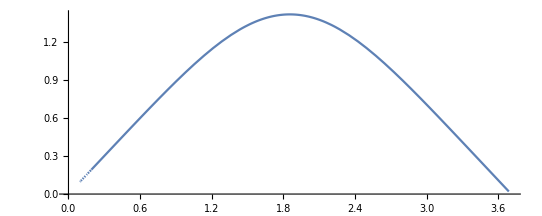

```mathematica
Plot[-2 √(-ⅈ Cos[2 JacobiAmplitude[((1+ⅈ) n-2 EllipticK[1/2])/(2 √2),2]]) Csc[2 JacobiAmplitude[((1+ⅈ) n-2 EllipticK[1/2])/(2 √2),2]],{n,0,3.71},AspectRatio->Automatic]
```

```mathematica
conf[Infinity]
```

(2 √(2 π) Gamma[5/4])/Gamma[3/4]

```mathematica
%//N
```

3.70815

```mathematica
1/cohub[time[n]]
```

(2 ⅈ Tan[1/2 (-π-4 JacobiAmplitude[((1+ⅈ) n-2 EllipticK[1/2])/(2 √2),2])])/(√(ⅈ Sin[1/2 (-π-4 JacobiAmplitude[((1+ⅈ) n-2 EllipticK[1/2])/(2 √2),2])]))

```mathematica
%//FullSimplify
```

-2 √(-ⅈ Cos[2 JacobiAmplitude[((1+ⅈ) n-2 EllipticK[1/2])/(2 √2),2]]) Csc[2 JacobiAmplitude[((1+ⅈ) n-2 EllipticK[1/2])/(2 √2),2]]

```mathematica
$Assumptions=n>0&&t>0
```

n>0&&t>0

```mathematica
1/3600*.3
```

0.0000833333

```mathematica
.31/(8.4*10^-5)
```

3690.48

```mathematica
2.47/.704^2
```

4.9837

```mathematica
(.112+.0225)/.704^2
```

0.271379

```mathematica
Solve[(-1+ⅈ) (√2 EllipticF[1/4 (π-2 ⅈ t),2]-EllipticK[1/2])==n,t]
```

{{t→-1/2 ⅈ (π+4 JacobiAmplitude[((1/2+ⅈ/2) n)/(√2)-EllipticK[1/2]/(√2),2])}}